# Numerical solution for cooperativity

### Python program to calculate stochastic matrix

```mathematica
ExternalEvaluate["Python", 
"import numpy as np
def decimalToBinary(n):
    # converting decimal to
    # and removng the prefix 0b
    return bin(n).replace(\"0b\",\"\")

def intVectorToBinNumMatrix(nums):
    # https://www.w3resource.com/python-exercises/numpy/python-numpy-exercise-187.php
    # converting a vector of integer numbers
    # into a matrix whose row are the representations
    # of those integer numbers in the binary system
    # Ex.: [1,2,3] => [[0,1],[1,0],[1,1]]
    max = np.max(nums)
    dimRow = int(round(np.log(max)/np.log(2)))
    return ((nums.reshape(-1,1) & (2**np.arange(dimRow))) != 0).astype(int)

def occVector(microstateMatrix):
    # extracts the occupancy vector from the microstate Matrix
    # Ex.: [[0,0],[1,0],[0,1],[1,1]] => [0,1,1,2]
    size = len(microstateMatrix)
    return np.array([np.dot(microstateMatrix[i],microstateMatrix[i]) \\
                     for i in range(size)])
    
def position(occupationVector, n):
    # find position of \"n\" inside vector occupationVector
    return np.array(np.where(occupationVector == n)[0])

def detDownStates(microstate):
    # identifies the microstates with occupationNum-1 from which the given 
    # microstate can be created by the adsorption of one stator
    # Ex. 1011 => [0011,1001,1010]
    # How it works: select among all microstates with occupationNum-1 those
    # for which their scalar product with the given microstate
    # equals occupationNum-1
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum > 0
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum-1)) 
    downStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum-1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum-1:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            downStates.append(input)
    return np.reshape(np.array(downStates),-1)                


def detUpStates(microstate):
    # identifies the microstates with occupationNum+1 from which the given 
    # microstate can be created by the desorption of one stator
    # Ex. 1011 => [1001,1010,0011]
    # How it works: select among all microstates with occupationNum+1 those
    # for which their scalar product with the given microstate
    # equals occupationNum
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum < Nmax
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum+1)) 
    upStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum+1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            upStates.append(input)
    return np.reshape(np.array(upStates),-1)


def stoMatFill(microstateMatrix, stoMatrix, microstateNum):
    # CORE ROUTINE: creates the row of the stochastic matrix corresponding
    # to the microstate microstateNum
    
    lenB = len(microstateMatrix[1]); lenSM = len(stoMatrix)
    
    assert isinstance(microstateNum,int)
    assert microstateNum > -1
    assert microstateNum < lenSM

    # first row corresponding to the single zero-occupation microstate
    if microstateNum == 0:
        # loss
        stoMatrix[0,0] = -lenB*a0
        # gain
        for i in range(len(position(occupationVector,1))):
            stoMatrix[0,position(occupationVector,1)[i]] = b0
            
    # last row corresponding to the single full-occupation microstate
    elif microstateNum == lenSM-1:
        # loss
        stoMatrix[lenSM-1,lenSM-1] = -lenB*b2
        # gain (remember PBC)
        for i in range(len(position(occupationVector,lenB-1))):
            stoMatrix[lenSM-1,position(occupationVector,lenB-1)[i]] = a2
    
    # fill the bulk of the matrix ... this is the diffult part
    else:
        
        # State we are looking at
        
        i = microstateNum
        
        state = microstateMatrix[i]
        
        # Down states
        dstates = detDownStates(state)
    
        # Up states
        ustates = detUpStates(state)
        
        
        for l in range(Nmax):
            
            if(state[l]==0):
            
                if(l==0):
                        
                    # No neigbours
                    if(state[Nmax-1] == state[l+1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0
                
                    # One neighbour
                    elif(state[Nmax-1] != state[l+1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[Nmax-1] == state[l+1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                    
                elif(l==Nmax-1):
                
                    # No neigbours
                    if(state[0] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0
                
                    # One neighbour
                    elif(state[0] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[0] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                        
                else:
                 
                    # No neigbours
                    if(state[l+1] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a0                    
                    # One neighbour
                    elif(state[l+1] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - a1
                
                    # Two neighbours
                    elif(state[l+1] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - a2
                        
            if(state[l]==1):
            
                if(l==0):
                        
                    # No neigbours
                    if(state[Nmax-1] == state[l+1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0
                
                    # One neighbour
                    elif(state[Nmax-1] != state[l+1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[Nmax-1] == state[l+1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                    
                elif(l==Nmax-1):
                
                    # No neigbours
                    if(state[0] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0
                
                    # One neighbour
                    elif(state[0] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[0] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                        
                else:
                 
                    # No neigbours
                    if(state[l+1] == state[l-1] == 0):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b0                    
                    # One neighbour
                    elif(state[l+1] != state[l-1]):
                    
                        stoMatrix[i,i] = stoMatrix[i,i] - b1
                
                    # Two neighbours
                    elif(state[l+1] == state[l-1] == 1):
                
                        stoMatrix[i,i] = stoMatrix[i,i] - b2
                    
                    
        # Loop for study of the down states            
        for k in range(len(dstates)):
        
            # Row of the microstate matrix of the transition state
            j = dstates[k]
            
        
            # Transition state we are looking at
            transState = microstateMatrix[j]
        
            # Which site has gain a stator 
            # final state - old state
            UpTrans = state - transState
        
            for l in range(Nmax):
            
                # There is a jump from the transition state to the state: 0 -> 1
                # We study then the neighbours of the transition state
                if(UpTrans[l] == 1):
                
                    if(l==0):
                    
                        # No neigbours
                        if(transState[Nmax-1] == transState[l+1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                    
                        # One neighbour
                        elif(transState[Nmax-1] != transState[l+1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[Nmax-1] == transState[l+1] == 1):
                    
                            stoMatrix[i,j] =  a2
                        
                    elif(l==Nmax-1):
                    
                        # No neigbours
                        if(transState[0] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                        # One neighbour
                        elif(transState[0] != transState[l-1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[0] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = a2
                    
                    else:
                     
                        # No neigbours
                        if(transState[l+1] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = a0
                    
                        # One neighbour
                        elif(transState[l+1] != transState[l-1]):
                        
                            stoMatrix[i,j] = a1
                    
                        # Two neighbours
                        elif(transState[l+1] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = a2
        
        # Loop for studying the upstates                    
        for k in range(len(ustates)):
        
            # Row of the microstate matrix of the transition state
            j = ustates[k]
        
            # Transition state we are looking at
            transState = microstateMatrix[j]
        
            # Which site has gain or loose a stator 
            # final state - old state
            UpTrans = transState - state
        
            DownTrans = state - transState
        
            for l in range(Nmax):
            
                             
                # There is a jump from the transition state to the state: 1 -> 0
                # We study then the neighbours of the transition state            
                if(DownTrans[l]== -1):
                
                    if(l==0):
                    
                        # No neigbours
                        if(transState[Nmax-1] == transState[l+1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[Nmax-1] != transState[l+1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[Nmax-1] == transState[l+1] == 1):
                    
                            stoMatrix[i,j] = b2
                        
                    elif(l==Nmax-1):
                    
                        # No neigbours
                        if(transState[0] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[0] != transState[l-1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[0] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = b2
                    
                    else:
                     
                        # No neigbours
                        if(transState[l+1] == transState[l-1] == 0):
                        
                            stoMatrix[i,j] = b0
                    
                        # One neighbour
                        elif(transState[l+1] != transState[l-1]):
                        
                            stoMatrix[i,j] = b1
                    
                        # Two neighbours
                        elif(transState[l+1] == transState[l-1] == 1):
                    
                            stoMatrix[i,j] = b2
            
        
    return stoMatrix
        
def testStoMatrix(stoMatrix,tolerance):
    # Function for testing that all colums sum 0
    
    Tsum = np.zeros(len(enumMicrostates))

    for i in range(len(enumMicrostates)):
        
        Tsum[i] = sum(stoMatrix[:,i])
        
        if(Tsum[i]<tolerance):
            
            Tsum[i] = 0.0
        
    if(sum(Tsum)==0):
        
        return print(\"True\")
    
\"\"\" Control parameters \"\"\"
# number of binding sites (> 2 needed to avoid ambiguity with PBC)
Nmax = 13
#assert Nmax > 2, f\"number greater than 2 expected, got: Nmax = {Nmax}\"

# kinetic rates
J = 0.0
mu = 1.0

a0 = 1./2.*(1 - np.tanh(-mu/2.))
b0 =  1./2.*(1 - np.tanh(mu/2.))

a1 = 1./2.*(1 - np.tanh(-(J + mu)/2.))
b1 = 1./2.*(1 - np.tanh((J + mu)/2.))

a2 = 1./2.*(1 - np.tanh(-J-mu/2.))
b2 = 1./2.*(1 - np.tanh(J+mu/2.))

enumMicrostates =  np.arange(0,2**Nmax)
microstateMatrix = intVectorToBinNumMatrix(enumMicrostates)
occupationVector = occVector(microstateMatrix)

# initialize stochastic matrix
stoMatrix = np.zeros([len(microstateMatrix),len(microstateMatrix)])

# fill the matrix
for i in range(len(enumMicrostates)):
    
    stoMatFill(microstateMatrix, stoMatrix,i)

# test if colums sum zero
testStoMatrix(stoMatrix,1e-10)
stoMatrix
"
]
```

True

NumericArray[<8192,8192>, Real64]

```mathematica
(M = Normal[%]) // MatrixForm;
```

```mathematica
ExternalEvaluate["Python", 
"import numpy as np
def decimalToBinary(n):
    # converting decimal to
    # and removng the prefix 0b
    return bin(n).replace(\"0b\",\"\")

def intVectorToBinNumMatrix(nums):
    # https://www.w3resource.com/python-exercises/numpy/python-numpy-exercise-187.php
    # converting a vector of integer numbers
    # into a matrix whose row are the representations
    # of those integer numbers in the binary system
    # Ex.: [1,2,3] => [[0,1],[1,0],[1,1]]
    max = np.max(nums)
    dimRow = int(round(np.log(max)/np.log(2)))
    return ((nums.reshape(-1,1) & (2**np.arange(dimRow))) != 0).astype(int)

def occVector(microstateMatrix):
    # extracts the occupancy vector from the microstate Matrix
    # Ex.: [[0,0],[1,0],[0,1],[1,1]] => [0,1,1,2]
    size = len(microstateMatrix)
    return np.array([np.dot(microstateMatrix[i],microstateMatrix[i]) \\
                     for i in range(size)])
    
def position(occupationVector, n):
    # find position of \"n\" inside vector occupationVector
    return np.array(np.where(occupationVector == n)[0])

def detDownStates(microstate):
    # identifies the microstates with occupationNum-1 from which the given 
    # microstate can be created by the adsorption of one stator
    # Ex. 1011 => [0011,1001,1010]
    # How it works: select among all microstates with occupationNum-1 those
    # for which their scalar product with the given microstate
    # equals occupationNum-1
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum > 0
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum-1)) 
    downStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum-1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum-1:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            downStates.append(input)
    return np.reshape(np.array(downStates),-1)                


def detUpStates(microstate):
    # identifies the microstates with occupationNum+1 from which the given 
    # microstate can be created by the desorption of one stator
    # Ex. 1011 => [1001,1010,0011]
    # How it works: select among all microstates with occupationNum+1 those
    # for which their scalar product with the given microstate
    # equals occupationNum
    
    # occupation number of MS
    occNum = microstate.sum(axis=0)
    assert occNum < Nmax
    assert len(microstate) < Nmax + 1
    
    # nb of microstates with occNum-1
    scan = len(position(occupationVector,occNum+1)) 
    upStates = []
    
    for i in range(scan):
        msTrans = microstateMatrix[position(occupationVector,occNum+1)][i]
        prod = np.dot(msTrans, microstate)
        if prod == occNum:
            #print(msTrans)
            input = np.where((microstateMatrix == msTrans).all(axis=1))[0]
            #print(input)
            upStates.append(input)
    return np.reshape(np.array(upStates),-1)

    
\"\"\" Control parameters \"\"\"
# number of binding sites (> 2 needed to avoid ambiguity with PBC)
Nmax = 13
#assert Nmax > 2, f\"number greater than 2 expected, got: Nmax = {Nmax}\"

enumMicrostates =  np.arange(0,2**Nmax)
microstateMatrix = intVectorToBinNumMatrix(enumMicrostates)
occupationVector = occVector(microstateMatrix)

occupationVector
"
]
```

NumericArray[…]

```mathematica
(arrayMicrostates = Normal[%]);
```

```mathematica
Nmax = 13;
```

```mathematica
Format[x[n_Integer]]:=Subscript[x,n]
Nt[t_,n:_Integer?Positive:2^Nmax]:=Array[x[#][t]&,n]
```

```mathematica
solRes = NDSolve[{Nt'[t]==M.Nt[t],Table[If[i==1,Nt[0][[i]]==1,Nt[0][[i]]==0],{i,1,2^Nmax}]},Nt[t],{t,0,10000}];
solRel = NDSolve[{Nt'[t]==M.Nt[t],Table[If[i==2^Nmax,Nt[0][[i]]==1,Nt[0][[i]]==0],{i,1,2^Nmax}]},Nt[t],{t,0,10000}];
```

```mathematica
solResT = Evaluate[Nt[t]/.solRes];
solRelT = Evaluate[Nt[t]/.solRel];
```

```mathematica
Plot[Evaluate[Nt[t]/.solRes],{t,0,1000},PlotRange->All]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Visualization`DiscontinuityDump`AnnotationQ[HoldForm].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of FreeQ[HoldComplete[InterpolatingFunction[{{0.,10000.}},{5,7,1,{165},{4},0,0,0,0,Automatic,«3»},{{0.,0.000140969,0.000281939,0.000563878,«4»,0.00958593,0.0124053,«155»}},{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«156»},{0.,0.,0.,0.,0.,0.,0.,0.,4.90512×10^-26,3.47956×10^-22,«320»}},{Automatic}][t]],«1»].

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

Identity::argx: Identity called with 4096 arguments; 1 argument is expected.

General::stop: Further output of Identity::argx will be suppressed during this calculation.

-Graphics-

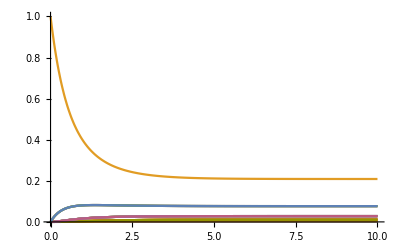

```mathematica
Plot[Evaluate[Nt[t]/.solRel],{t,0,10},PlotRange->All]
```

```mathematica
SSRes[t_]:= Sum[solResT[[1]][[k]]*arrayMicrostates[[k]],{k,1,Length[solResT[[1]]]}]
sdRes[t_]:=Sqrt[Sum[solResT[[1]][[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solResT[[1]]]}]-SSRes[t]^2]
SSRel[t_]:= Sum[solRelT[[1]][[k]]*arrayMicrostates[[k]],{k,1,Length[solRelT[[1]]]}]
sdRel[t_]:=Sqrt[Sum[solRelT[[1]][[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solRelT[[1]]]}]-SSRel[t]^2]
```

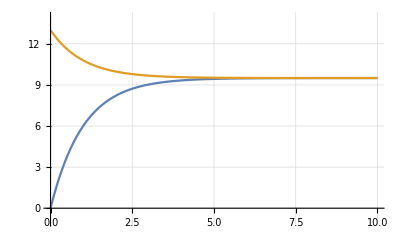

```mathematica
Plot[{SSRes[t],SSRel[t]},{t,0,10},PlotRange->{{0,10},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"]
```

```mathematica
MR = Rationalize[M,10^-15];
```

```mathematica
{lu,p,c} = LUDecomposition[MR];
{l,u}= {LowerTriangularize[lu,-1]+IdentityMatrix[2^Nmax], u = UpperTriangularize[lu]};
```

```mathematica
l.u == MR[[p]]
```

True

```mathematica
NtT[t_,n:_Integer?Positive:2^Nmax]:=Array[x[#][t]&,n]
```

```mathematica
v = NtT[t];
b = NtT'[t];
system  = {MR.v==b};
```

```mathematica
Format[y[n_Integer]]:=Subscript[y,n];
νt[t_,n:_Integer?Positive:2^Nmax]:=Array[y[#][t]&,n];
```

```mathematica
tri1 = Reverse[Thread[u.v == νt[t]]];
Column[tri1];
```

```mathematica
tri2 = Thread[l.νt[t]==NtT'[t]];
Column[tri2];
```

### Diagonalisation of matrix

```mathematica
Nmax=5;
```

```mathematica
(U = Transpose[Eigenvectors[MR]]) // Chop;
(Ui = Inverse[U]) // Chop;
```

```mathematica
Λ = Ui.MR.U // Chop // MatrixForm
```

(-5. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -4. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Solution of the decoupled system of linear ODEs

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[MR][[k]]*t],{k,1,Length[MR]}]
solDiago[t]//Chop//MatrixForm;
```

### Solution of the original system of linear ODEs

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
(IC=solOri/. t-> 0)//MatrixForm;
```

### Initial conditions

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

### Find special solution equivalent to resurrection

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]] // Chop;
```

```mathematica
solSpecialRes = solOri/.resCond//Flatten;
```

```mathematica
ssSpecialRes = solSpecialRes /.t->500;
```

General::munfl: Exp[-1500.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
solRes = Table[0,Nmax+1];
For[i=0,i<= Nmax,i++,
For[j=1, j<=Length[solSpecialRes],j++,
If[arrayMicrostates[[j]]==i, solRes[[i+1]] = solRes[[i+1]]+ ssSpecialRes[[j]]]]]
Print[solRes // Chop//MatrixForm]
```

(0.00140698
0.0191229
0.103963
0.2826
0.384093
0.208815)

```mathematica
Sum[solRes[[k]],{k,1,Nmax+1}]
```

1.

```mathematica
Sum[solSpecialRes[[k]],{k,1,Length[solSpecialRes]}]/.t->500
```

General::munfl: Exp[-1500.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.

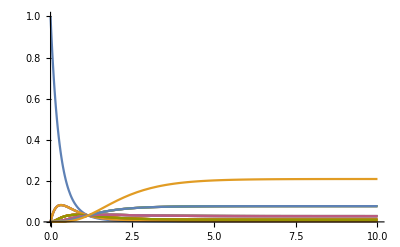

```mathematica
Tmax=10;
Plot[{solSpecialRes},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Find special solution equivalent to release after stall

```mathematica
relCond = Solve[Table[IC[[k]]==If[arrayMicrostates[[k]]==Nmax,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]] // Chop;
```

```mathematica
solSpecialRel = solOri/.relCond//Flatten;
```

```mathematica
ssSpecialRel = solSpecialRel /.t->100 // Flatten;
```

General::munfl: (-5.39644×10^-10+0. ⅈ) (9.85968×10^-305+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (5.39644×10^-10+0. ⅈ) (9.85968×10^-305+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
solRel = Table[0,Nmax+1];
For[i=0,i<= Nmax,i++,
For[j=1, j<=Length[solSpecialRel],j++,
If[arrayMicrostates[[j]]==i, solRel[[i+1]] = solRel[[i+1]]+ ssSpecialRel[[j]]]]]
Print[solRel // MatrixForm]
```

(5.39644×10^-10-2.76302×10^-67 ⅈ
7.58733×10^-8-3.30212×10^-65 ⅈ
4.57187×10^-6-1.6387×10^-63 ⅈ
0.000153047-4.31052×10^-62 ⅈ
0.00307404-6.29759×10^-61 ⅈ
0.0370462-4.74479×10^-60 ⅈ
0.248031-1.27225×10^-59 ⅈ
0.711691+1.81419×10^-59 ⅈ)

```mathematica
Sum[solSpecialRel[[k]],{k,1,Length[solSpecialRel]}]/.t->100
```

General::munfl: (3.14329×10^-23+0. ⅈ) (9.85968×10^-305+0. ⅈ) is too small to represent as a normalized machine number; precision may be lost.

1.+1.19739×10^-63 ⅈ

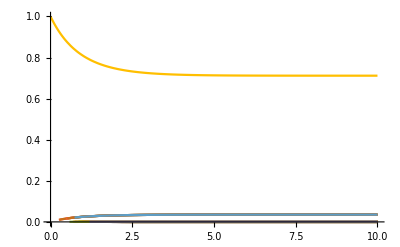

```mathematica
Tmax=10;
Plot[{solSpecialRel},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

### Stationary solution

```mathematica
solSpecialRes/. t-> 100000//MatrixForm;
```

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-400000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-300000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
mRes[t_]:= Sum[solSpecialRes[[k]]*arrayMicrostates[[k]],{k,1,Length[solSpecialRes]}]
sdRes[t_]:=Sqrt[Sum[solSpecialRes[[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solSpecialRes]}]-mRes[t]^2]
```

```mathematica
mRel[t_]:= Sum[solSpecialRel[[k]]*arrayMicrostates[[k]],{k,1,Length[solSpecialRel]}]
sdRel[t_]:=Sqrt[Sum[solSpecialRel[[k]]*arrayMicrostates[[k]]^2,{k,1,Length[solSpecialRel]}]-mRel[t]^2]
```

```mathematica
Tmax=10;
plot=Show[Plot[{mRes[t],mRel[t]},{t,0,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"],RegionPlot[{mRes[t]-sdRes[t]<y && y<mRes[t]+sdRes[t],mRel[t]-sdRel[t]<y && y<mRel[t]+sdRel[t]},{t,0.1,Tmax},{y,-1,Nmax+1},BoundaryStyle->{Dotted,Thickness[0]}],ImageSize->Large]
```

$Aborted

```mathematica
mRes[t]/. t -> 1000
```

General::munfl: Exp[-7000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.331981